```mathematica
DSolve[y'[x]==x/y[x],y[x],x]
```

{{y[x]→-√(x^2+2 C[1])},{y[x]→√(x^2+2 C[1])}}

```mathematica
(* y^2/2 = x^2/2 + C[1] *)
```

```mathematica
g[x_]=√(x^2+2 C[1]);
```

```mathematica
Solve[g[3]==5,C[1]]
```

{{C[1]→8}}

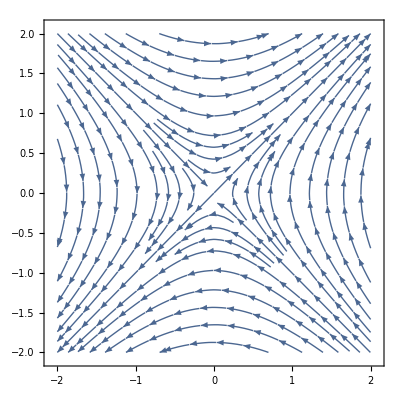

```mathematica
directionField=StreamPlot[{y,x},{x,-2,2},{y,-2,2}]
```

```mathematica
(* dy/dx = x/y *)
```

```mathematica
(* dy = (x/y)dx = *)
```

```mathematica
(* y dy = x dx *)
```

```mathematica
Integrate[y,y]
```

y^2/2

```mathematica
∫y ⅆy
```

y^2/2

```mathematica
DSolve[y'[x]==3 x^2 y[x]^2-y[x]^2,y[x],x]
```

{{y[x]→1/(x-x^3-C[1])}}

```mathematica
(* Exemplo 2 pg. 361 *)
```

```mathematica
(* dy/dx = √(x y) *)
```

```mathematica
(* dy = √(x y) dx*)
```

```mathematica
(* dy = √x √y dx*)
```

```mathematica
DSolve[y'[x]==√(x  y[x]),y[x],x]
```

DSolve[True,y[x],x]